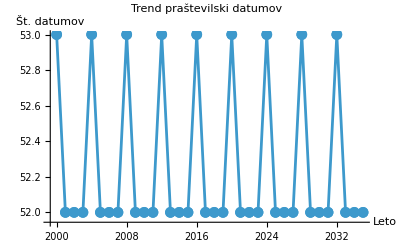

```mathematica
(*Matematično zanimivi datumi-analiza in prikaz*)
(*Ta beležnica analizira in prikazuje posebne datume:praštevilske,palindromske in lunine faze.Rezultati so prikazani interaktivno in grafično.*)
(*1. Funkcija za lunine faze*)
offlineMoonPhase[datum_]:=Module[{day=AbsoluteTime[datum],moonPeriod=29.53*24*3600,illumination,phaseName},illumination=0.5+0.5*Sin[(2*Pi*(day-AbsoluteTime[{2001,1,1}]))/moonPeriod];
phaseName=Which[illumination<0.1,"Mlada luna",illumination<0.6,"Prva krajec",illumination<0.9,"Polna luna",True,"Zadnji krajec"];
<|"Datum"->DateString[datum,{"Day",".","Month",".","Year"}],"Faza Lune"->phaseName,"Osvetljenost (%)"->NumberForm[illumination*100,{3,1}]|>];

(*2. Praštevilski datumi*)
primeDates[leto_]:=Module[{dni},dni=Select[DateRange[DateObject[{leto,1,1}],DateObject[{leto,12,31}],"Day"],PrimeQ[DateValue[#,"Day"]]&&PrimeQ[DateValue[#,"Month"]]&];
DateString[#,{"Day",".","Month",".","Year"}]&/@dni];

(*3. Palindromski datumi*)
palindromDates[leto_]:=Module[{dni,datStr},dni=DateRange[DateObject[{leto,1,1}],DateObject[{leto,12,31}],"Day"];
Select[dni,(datStr=DateString[#,{"Day",".","Month",".","Year"}];datStr===StringReverse[datStr])&]];

(*4. Interaktivni prikaz*)
Manipulate[Column[{Style["Matematično zanimivi datumi v "<>ToString[leto],Bold,16],"• Praštevilski datumi:",primeDates[leto],"• Palindromski datumi:",DateString[#,{"Day",".","Month",".","Year"}]&/@palindromDates[leto],"• Lunina mena za izbrani dan:",offlineMoonPhase[DateObject[{leto,mesec,dan}]]}],{{leto,2025,"Leto"},1900,2100,1},{{mesec,1,"Mesec"},1,12,1},{{dan,1,"Dan"},1,31,1},TrackedSymbols:>{leto,mesec,dan}]


(*5. Grafični prikaz posebnih datumov*)
grafPosebnihDatumov[odLeto_,doLeto_]:=Module[{leta,stDat},leta=Range[odLeto,doLeto];
stDat=Length/@(primeDates/@leta);
ListLinePlot[Transpose[{leta,stDat}],PlotLabel->"Trend praštevilski datumov",AxesLabel->{"Leto","Št. datumov"},Mesh->All,PlotMarkers->Automatic]];

grafPosebnihDatumov[2000,2035]
```